# Definitions of functions. To be placed in separate files.

```mathematica
<<FeynCalc`
<<DummyArray`
<<ITensor`
<<CTensor`
<<CITensor`
<<CIITensor`
<<CIIITensor`
<<ETensor`
<<CETensor`
<<GravitonVertex`
<<GravitonScalarVertex`
<<GravitonFermionVertex`
<<GravitonVectorVertex`
<<ETensorC`
<<CETensorC`
<<CITensorC`
<<CIITensorC`
<<GravitonSUNYM`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

# Timings. To be separated .

I tensors.

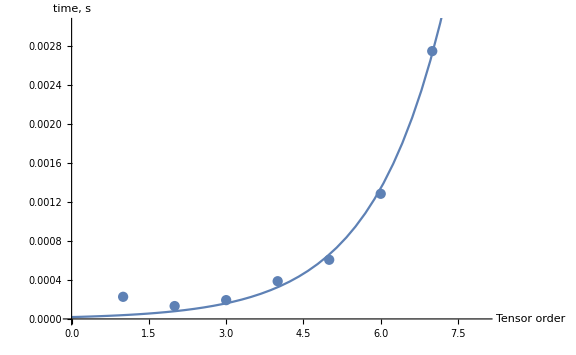

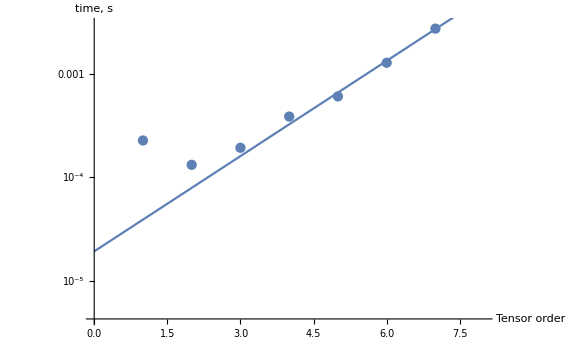

```mathematica
Table[Timing[ITensor[DummyArray[i]]][[1]],{i,1,7}];
τ Exp[t/T]/.FindFit[%,τ Exp[t/T],{τ,T},t];
Show[{ListPlot[%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%]+1},{0,1.1Max[%%]}}],Plot[%,{t,0,Length[%%]+2},PlotLegends->%]}]
Show[{ListLogPlot[%%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%%]+1},{0,1.1Max[%%%]}}],LogPlot[%%,{t,0,Length[%%%]+2},PlotLegends->%%]}]
```

C tensor.

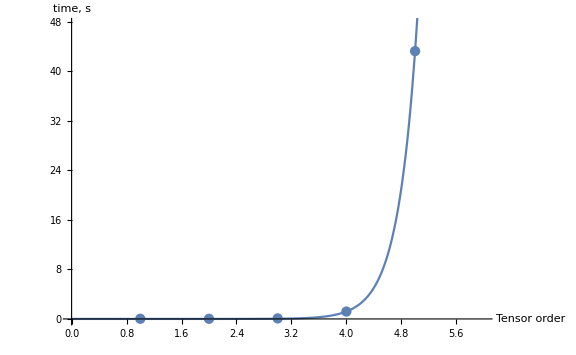

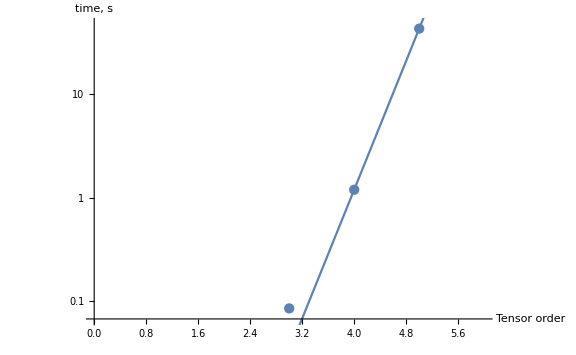

```mathematica
Table[Timing[CTensor[DummyArray[i]]][[1]],{i,1,5}];
τ Exp[t/T]/.FindFit[%,τ Exp[t/T],{τ,T},t];
Show[{ListPlot[%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%]+1},{0,1.1Max[%%]}}],Plot[%,{t,0,Length[%%]+2},PlotLegends->%]}]
Show[{ListLogPlot[%%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%%]+1},{0,1.1Max[%%%]}}],LogPlot[%%,{t,0,Length[%%%]+2},PlotLegends->%%]}]
```

CIII tensor.

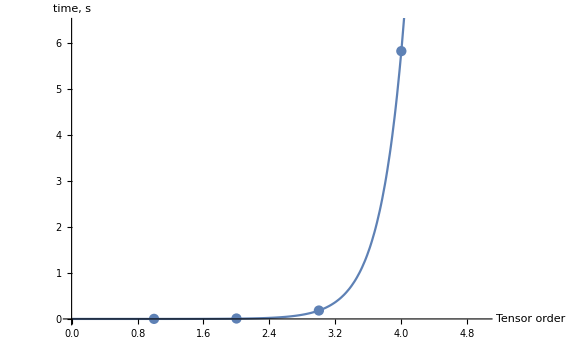

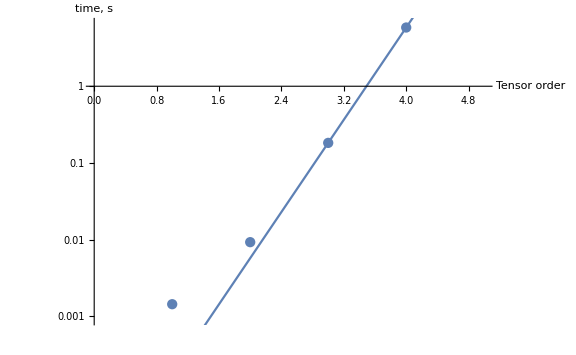

```mathematica
Table[Timing[CIIITensor[{μ,ν,α,β,ρ,σ},dummyArray[i]]][[1]],{i,1,4}];
τ Exp[t/T]/.FindFit[%,τ Exp[t/T],{τ,T},t];
Show[{ListPlot[%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%]+1},{0,1.1Max[%%]}}],Plot[%,{t,0,Length[%%]+2},PlotLegends->%]}]
Show[{ListLogPlot[%%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%%]+1},{0,1.1Max[%%%]}}],LogPlot[%%,{t,0,Length[%%%]+2},PlotLegends->%%]}]
```

Graviton vertex.

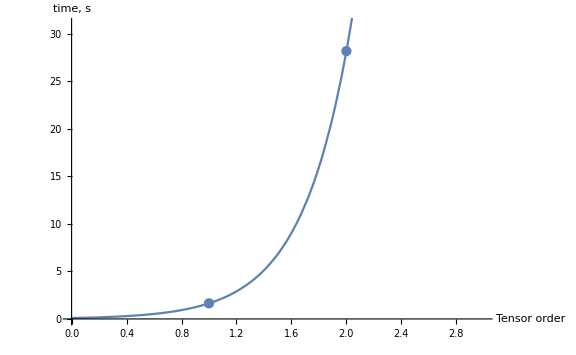

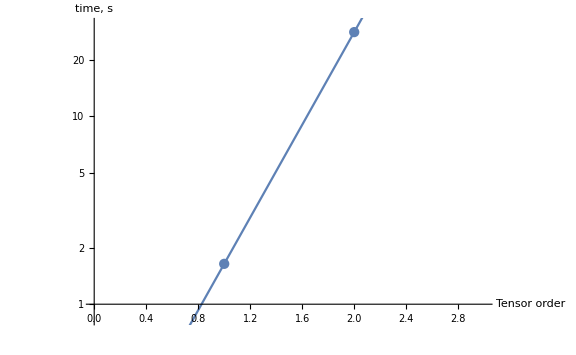

```mathematica
Table[Timing[GravitonVertex[Flatten[Function[{ToExpression["m"<>ToString[#]],ToExpression["n"<>ToString[#]],ToExpression["p"<>ToString[#]]}]/@Range[i]]]][[1]],{i,3,4}];
τ Exp[t/T]/.FindFit[%,τ Exp[t/T],{τ,T},t];
Show[{ListPlot[%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%]+1},{0,1.1Max[%%]}}],Plot[%,{t,0,Length[%%]+2},PlotLegends->%]}]
Show[{ListLogPlot[%%%,ImageSize->Large,AxesLabel->{"Tensor order","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%%]+1},{0,1.1Max[%%%]}}],LogPlot[%%,{t,0,Length[%%%]+2},PlotLegends->%%]}]
```

Graviton-scalar vertex.

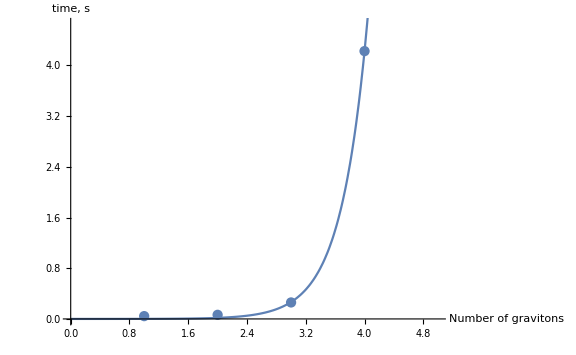

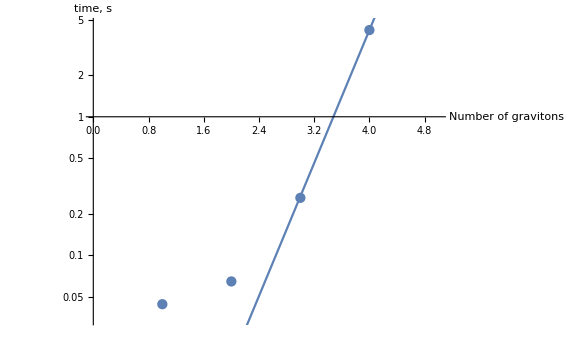

```mathematica
Table[Timing[GravitonScalarVertex[Join[dummyArray[i],{p1,p2}]]][[1]],{i,1,4}];
τ Exp[t/T]/.FindFit[%,τ Exp[t/T],{τ,T},t];
Show[{ListPlot[%%,ImageSize->Large,AxesLabel->{"Number of gravitons","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%]+1},{0,1.1Max[%%]}}],Plot[%,{t,0,Length[%%]+2},PlotLegends->%]}]
Show[{ListLogPlot[%%%,ImageSize->Large,AxesLabel->{"Number of gravitons","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%%]+1},{0,1.1Max[%%%]}}],LogPlot[%%,{t,0,Length[%%%]+2},PlotLegends->%%]}]
```

Graviton-vector vertex.

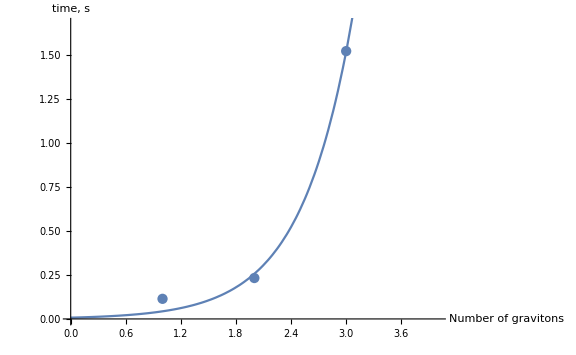

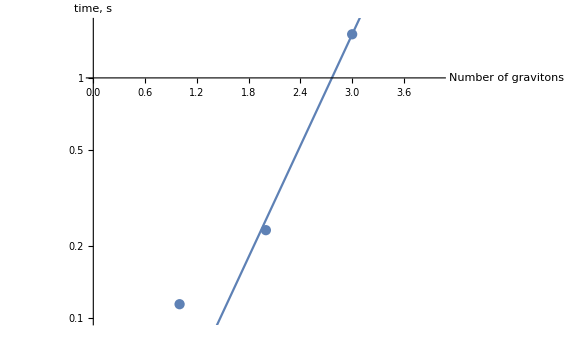

```mathematica
Table[Timing[GravitonVectorVertex[Join[dummyArray[i],{λ1,λ2,p1,p2}]]][[1]],{i,1,3}];
τ Exp[t/T]/.FindFit[%,τ Exp[t/T],{τ,T},t];
Show[{ListPlot[%%,ImageSize->Large,AxesLabel->{"Number of gravitons","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%]+1},{0,1.1Max[%%]}}],Plot[%,{t,0,Length[%%]+2},PlotLegends->%]}]
Show[{ListLogPlot[%%%,ImageSize->Large,AxesLabel->{"Number of gravitons","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%%]+1},{0,1.1Max[%%%]}}],LogPlot[%%,{t,0,Length[%%%]+2},PlotLegends->%%]}]
```

Graviton-fermion vertex.

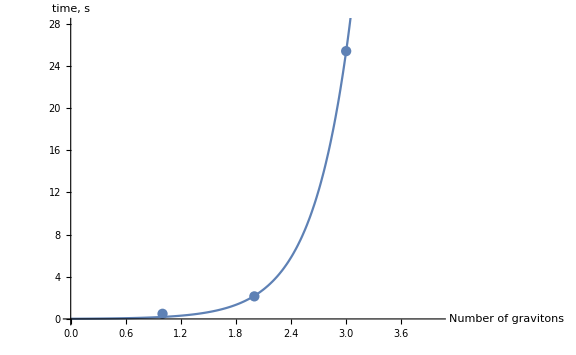

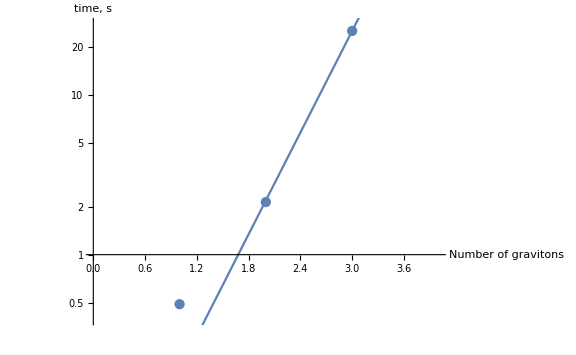

```mathematica
Table[Timing[GravitonFermionVertex[Join[dummyArray[i],{λ1,λ2,p1,p2}]]][[1]],{i,1,3}];
τ Exp[t/T]/.FindFit[%,τ Exp[t/T],{τ,T},t];
Show[{ListPlot[%%,ImageSize->Large,AxesLabel->{"Number of gravitons","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%]+1},{0,1.1Max[%%]}}],Plot[%,{t,0,Length[%%]+2},PlotLegends->%]}]
Show[{ListLogPlot[%%%,ImageSize->Large,AxesLabel->{"Number of gravitons","time, s"},AxesOrigin->{0,0},PlotRange->{{0,Length[%%%]+1},{0,1.1Max[%%%]}}],LogPlot[%%,{t,0,Length[%%%]+2},PlotLegends->%%]}]
```

# Export procedures.

```mathematica
<<FeynCalc`
<<DummyArray`
<<ITensor`
<<CTensor`
<<CITensor`
<<CIITensor`
<<CIIITensor`
<<ETensor`
<<CETensor`
<<GravitonVertex`
<<GravitonScalarVertex`
<<GravitonFermionVertex`
```

## Procedures that perform export of interaction vertices.

This command set the working directory to be the directory where this file is placed.

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/latosh_boris/.Mathematica/Applications/FeynGrav/Libs

Export of graviton vertices up to order 𝒪(κ^order).

```mathematica
exportGravitonVertex[order_] := Module[{cursor}, 
Print["Export of graviton vertices is initiated."];
For[cursor=3,cursor≤order+2,cursor++,
Evaluate[GravitonVertex[Flatten[Function[{ToExpression["m"<>ToString[#]],ToExpression["n"<>ToString[#]],ToExpression["p"<>ToString[#]]}]/@Range[cursor]]]]>>"GravitonVertex_"<>ToString[cursor-2];
Print["Done for order "<>ToString[cursor-2]];
]
]
```

Export of graviton-scalar vertices up to order 𝒪(κ^order).

```mathematica
exportGravitonScalarVertex[order_]:=Module[{cursor},
Print["Export of graviton-scalar vertices is initiated."];
	For[cursor=1,cursor<=order,cursor++,
	Evaluate[GravitonScalarVertex[Join[dummyArray[cursor],{p1,p2}]]]>>"GravitonScalarVertex_"<>ToString[cursor];
	Print["Done for order "<>ToString[cursor]];
	];
Print["Export of graviton-massive scalar vertices is initiated."];
	For[cursor=1,cursor<=order,cursor++,
	Evaluate[GravitonMassiveScalarVertex[Join[dummyArray[cursor],{p1,p2}],m]]>>"GravitonMassiveScalarVertex_"<>ToString[cursor];
	Print["Done for order "<>ToString[cursor]];
	];
]
```

Export of graviton-vector vertices up to order 𝒪(κ^order).

```mathematica
exportGravitonVectorVertex[order_]:=Module[{cursor},
	Print["Export of graviton-vector vertices is initiated."];
	For[cursor=1,cursor<=order,cursor++,
		Evaluate[GravitonVectorVertex[Join[dummyArray[cursor],{λ1,λ2,p1,p2}]]]>>"GravitonVectorVertex_"<>ToString[cursor];
		Print["Done for order "<>ToString[cursor]];
	];
Print["Export of graviton-massive vector vertices is initiated."];
	For[cursor=1,cursor<=order,cursor++,
		Evaluate[GravitonMassiveVectorVertex[Join[dummyArray[cursor],{λ1,λ2,p1,p2}],m]]>>"GravitonMassiveVectorVertex_"<>ToString[cursor];
		Print["Done for order "<>ToString[cursor]];
	]
]
```

Export of graviton-fermion vertices up to order 𝒪(κ^order).

```mathematica
exportGravitonFermionVertex[order_]:=Module[{cursor},
	Print["Export of graviton-fermion vertices is initiated."];
	For[cursor=1,cursor<=order,cursor++,
		Evaluate[GravitonFermionVertex[Join[dummyArray[cursor],{p1,p2}]]]>>"GravitonFermionVertex_"<>ToString[cursor];
		Print["Done for order "<>ToString[cursor]];
	]
Print["Export of graviton-massive fermion vertices is initiated."];
	For[cursor=1,cursor<=order,cursor++,
		Evaluate[GravitonMassiveFermionVertex[Join[dummyArray[cursor],{p1,p2}],m]]>>"GravitonMassiveFermionVertex_"<>ToString[cursor];
		Print["Done for order "<>ToString[cursor]];
	]
]
```

Export of graviton-SU(N)YM vertices up to order 𝒪(κ^order).

```mathematica
exportGravitonSUNYMVertex[order_]:=Module[{cursor},
	Print["Export of graviton-quark-gluon vertices is initiated."];
	For[cursor=1,cursor<=order,cursor++,
		Evaluate[GravitonQuarkGluonVertex[Join[dummyArray[cursor],{μ,a}]]]>>"GravitonQuarkGluonVertex_"<>ToString[cursor];
		Print["Done for order "<>ToString[cursor]];
	]
Print["Export of graviton-three-gluon vertices is initiated."];
	For[cursor=1,cursor<=order,cursor++,
		Evaluate[GravitonThreeGluonVertex[Join[dummyArray[cursor],{p1,μ1,a1,p2,μ2,a2,p3,μ3,a3}]]]>>"GravitonThreeGluonVertex_"<>ToString[cursor];
		Print["Done for order "<>ToString[cursor]];
	]
Print["Export of graviton-four-gluon vertices is initiated."];
	For[cursor=1,cursor<=order,cursor++,
		Evaluate[GravitonFourGluonVertex[Join[dummyArray[cursor],{p1,μ1,a1,p2,μ2,a2,p3,μ3,a3,p4,μ4,a4}]]]>>"GravitonFourGluonVertex_"<>ToString[cursor];
		Print["Done for order "<>ToString[cursor]];
	]
]
```

## The actual export. Do not run without a necessity!

The following module runs the export procedure. The export is performed up to the order 𝒪(κ^order).

```mathematica
Module[{order},
order =3;
exportGravitonVertex[order];
exportGravitonScalarVertex[order];
exportGravitonVectorVertex[order];
exportGravitonFermionVertex[order];
exportGravitonSUNYMVertex[order];
]
```